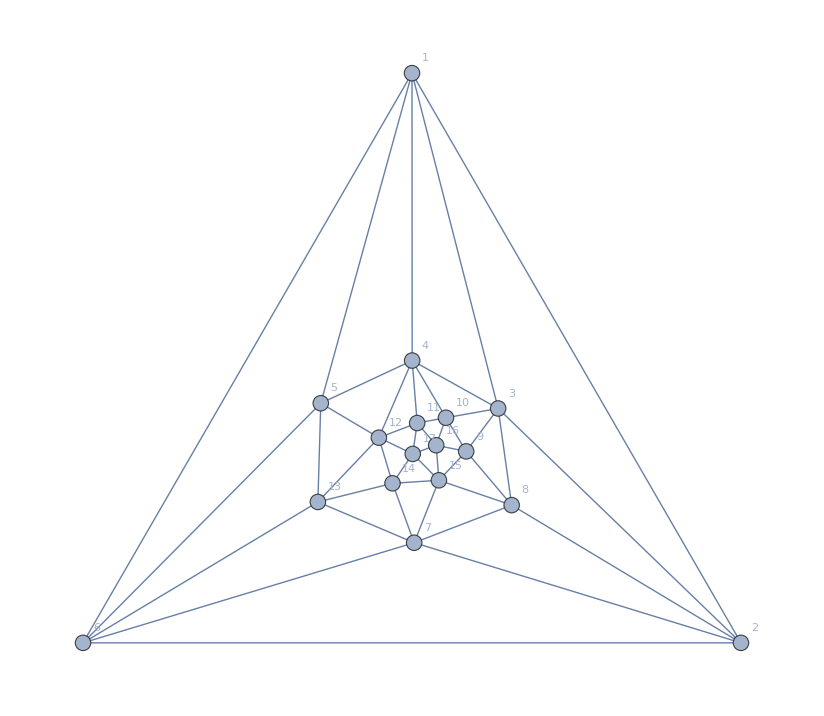

```mathematica
Graph[plantri[[8]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
EmbedGraph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
atomKeys
```

{29524,29525,29527,29533,29537,29551,29560,29605,29608,29633,29767,29768,29797,29857,29888,30253,30262,30334,30496,30586,31711,31714,31738,31954,31984,32441,32684,36085,36086,36112,36166,36194,36817,36898,38281,38308,39014,49207,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}
```

{36166,31738,29608,36112,31714}

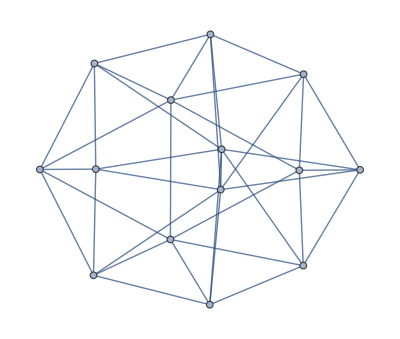

```mathematica
gr=EmbedGraph5Plantri8[allGraphs,gamma1Key]
```

```mathematica
PlanarGraphQ[gr]
```

False

```mathematica
Factor[ChromaticPolynomial[gr,x]]
```

(-4+x) (-3+x) (-2+x) (-1+x) x (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9)

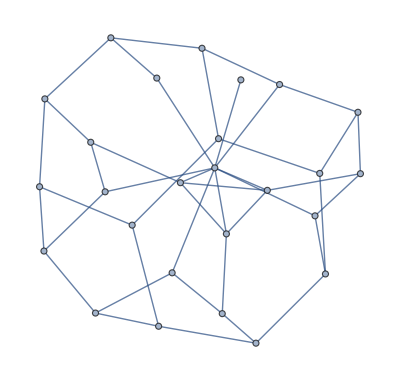

```mathematica
fr=DualGraph[Faces[gr]]
```

```mathematica
PlanarGraphQ[fr]
```

False

```mathematica
Factor[FlowPolynomial[fr,x]]
```

0

```mathematica
values=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
With[
{h=DualGraph[Faces[g]]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24,Factor[ChromaticPolynomial[g,x]],Factor[FlowPolynomial[g,x]],key}
]
]
,{key,Sort[atomKeys]}
]
,
key];
```

{v1x2x3x4x5→{-Graphics-,0,(-4+x) (-3+x) (-2+x) (-1+x) x (-1859948+4632058 x-5410091 x^2+3928457 x^3-1975462 x^4+722760 x^5-196118 x^6+39380 x^7-5718 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (699053232-5320785055 x+20944477374 x^2-56671930891 x^3+118008515466 x^4-200511351136 x^5+287699821850 x^6-356172103234 x^7+385849279766 x^8-369244281839 x^9+314126763213 x^10-238557717111 x^11+162127696592 x^12-98715334604 x^13+53845499625 x^14-26281072803 x^15+11451811457 x^16-4439526153 x^17+1523857317 x^18-460175478 x^19+121239916 x^20-27565784 x^21+5331393 x^22-860240 x^23+112702 x^24-11520 x^25+862 x^26-42 x^27+x^28),29524},v1x2x3x45→{-Graphics-,10,(-3+x)^2 (-2+x) (-1+x) x (374510-877901 x+958185 x^2-644057 x^3+295922 x^4-97127 x^5+23025 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (65274964-441073985 x+1525227437 x^2-3590244073 x^3+6444128922 x^4-9353646606 x^5+11360456483 x^6-11790401274 x^7+10596001972 x^8-8315072116 x^9+5726279898 x^10-3469390926 x^11+1850218044 x^12-867387542 x^13+356357323 x^14-127666092 x^15+39596670 x^16-10527323 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),29525},v1x2x35x4→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-105145829+723552773 x-2571907583 x^2+6272650847 x^3-11740440532 x^4+17861135058 x^5-22831532122 x^6+25029027171 x^7-23840293601 x^8+19897598205 x^9-14628806443 x^10+9502341654 x^11-5459544975 x^12+2773150866 x^13-1242789601 x^14+489608988 x^15-168645334 x^16+50407488 x^17-12940987 x^18+2814396 x^19-508772 x^20+74436 x^21-8472 x^22+704 x^23-38 x^24+x^25),29527},v1x2x34x5→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (363244-857798 x+942908 x^2-637598 x^3+294264 x^4-96865 x^5+23001 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (62126489-420777127 x+1459823135 x^2-3450337337 x^3+6221653587 x^4-9074574325 x^5+11074457871 x^6-11545682533 x^7+10418798564 x^8-8205642063 x^9+5668453921 x^10-3443251695 x^11+1840148695 x^12-864106451 x^13+355463504 x^14-127466028 x^15+39560800 x^16-10522366 x^17+2366271 x^18-441580 x^19+66597 x^20-7804 x^21+667 x^22-37 x^23+x^24),29533},v1x2x345→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (207074-539221 x+645432 x^2-469488 x^3+230533 x^4-80003 x^5+19887 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-7881314+48314136 x-150787364 x^2+318608677 x^3-510076087 x^4+655295401 x^5-697930443 x^6+628309059 x^7-483671341 x^8+320467530 x^9-183294028 x^10+90501964 x^11-38475341 x^12+14009273 x^13-4332182 x^14+1123867 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),29537},v1x25x3x4→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-1746193+4433963 x-5258709 x^2+3861711 x^3-1956730 x^4+719298 x^5-195702 x^6+39350 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-112455233+769998143 x-2720435942 x^2+6590764307 x^3-12252164450 x^4+18517678931 x^5-23527423582 x^6+25651622110 x^7-24316661649 x^8+20211649723 x^9-14807811507 x^10+9590573044 x^11-5497053104 x^12+2786827851 x^13-1247030469 x^14+490713166 x^15-168882433 x^16+50448400 x^17-12946443 x^18+2814924 x^19-508805 x^20+74437 x^21-8472 x^22+704 x^23-38 x^24+x^25),29551},v1x25x34→{-Graphics-,31,(-3+x) (-2+x) (-1+x) x (337615-818648 x+917171 x^2-628070 x^3+292091 x^4-96555 x^5+22975 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15156445-94062187 x+299457067 x^2-649860369 x^3+1075306865 x^4-1436472121 x^5+1600447042 x^6-1516467548 x^7+1236586402 x^8-873870006 x^9+537087388 x^10-287346402 x^11+133630538 x^12-53818702 x^13+18655386 x^14-5515176 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),29560},v1x24x3x5→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-105145829+723552773 x-2571907583 x^2+6272650847 x^3-11740440532 x^4+17861135058 x^5-22831532122 x^6+25029027171 x^7-23840293601 x^8+19897598205 x^9-14628806443 x^10+9502341654 x^11-5459544975 x^12+2773150866 x^13-1242789601 x^14+489608988 x^15-168645334 x^16+50407488 x^17-12940987 x^18+2814396 x^19-508772 x^20+74436 x^21-8472 x^22+704 x^23-38 x^24+x^25),29605},v1x24x35→{-Graphics-,0,(-4+x) (-3+x) (-2+x) (-1+x) x (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9),(-2+x) (-1+x) (-24684780+156505923 x-513913455 x^2+1159863722 x^3-2009504511 x^4+2826214249 x^5-3330540610 x^6+3352101156 x^7-2915824383 x^8+2208033431 x^9-1461591084 x^10+847104979 x^11-429686274 x^12+190295195 x^13-73255375 x^14+24347591 x^15-6920210 x^16+1659824 x^17-329807 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),29608},v1x245x3→{-Graphics-,10,(-3+x) (-2+x) (-1+x) x (325870-797633 x+901442 x^2-621760 x^3+290658 x^4-96380 x^5+22966 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (14194264-88538644 x+283706608 x^2-620196409 x^3+1033964099 x^4-1391234908 x^5+1560233287 x^6-1486828242 x^7+1218264551 x^8-864321828 x^9+532892307 x^10-285799731 x^11+133156641 x^12-53699927 x^13+18631621 x^14-5511521 x^15+1372358 x^16-282478 x^17+46832 x^18-6015 x^19+562 x^20-34 x^21+x^22),29633},v1x23x4x5→{-Graphics-,10,(-3+x)^2 (-2+x) (-1+x) x (374510-877901 x+958185 x^2-644057 x^3+295922 x^4-97127 x^5+23025 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (65274964-441073985 x+1525227437 x^2-3590244073 x^3+6444128922 x^4-9353646606 x^5+11360456483 x^6-11790401274 x^7+10596001972 x^8-8315072116 x^9+5726279898 x^10-3469390926 x^11+1850218044 x^12-867387542 x^13+356357323 x^14-127666092 x^15+39596670 x^16-10527323 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),29767},v1x23x45→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (223754-569603 x+668793 x^2-479314 x^3+232975 x^4-80362 x^5+19916 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9111509+55389004 x-171024652 x^2+356838793 x^3-563455551 x^4+713694641 x^5-749707439 x^6+666263633 x^7-506937182 x^8+332454878 x^9-188485607 x^10+92383131 x^11-39040158 x^12+14147592 x^13-4359147 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),29768},v1x235x4→{-Graphics-,10,(-3+x) (-2+x) (-1+x) x (325870-797633 x+901442 x^2-621760 x^3+290658 x^4-96380 x^5+22966 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (14194264-88538644 x+283706608 x^2-620196409 x^3+1033964099 x^4-1391234908 x^5+1560233287 x^6-1486828242 x^7+1218264551 x^8-864321828 x^9+532892307 x^10-285799731 x^11+133156641 x^12-53699927 x^13+18631621 x^14-5511521 x^15+1372358 x^16-282478 x^17+46832 x^18-6015 x^19+562 x^20-34 x^21+x^22),29797},v1x234x5→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (207074-539221 x+645432 x^2-469488 x^3+230533 x^4-80003 x^5+19887 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-7881314+48314136 x-150787364 x^2+318608677 x^3-510076087 x^4+655295401 x^5-697930443 x^6+628309059 x^7-483671341 x^8+320467530 x^9-183294028 x^10+90501964 x^11-38475341 x^12+14009273 x^13-4332182 x^14+1123867 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),29857},v1x2345→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-56573+135522 x-147296 x^2+95722 x^3-41129 x^4+12147 x^5-2469 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1685376+9505266 x-27291707 x^2+52988994 x^3-77726010 x^4+91045256 x^5-87809474 x^6+70955633 x^7-48503117 x^8+28171041 x^9-13908250 x^10+5818796 x^11-2049117 x^12+600776 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),29888},v15x2x3x4→{-Graphics-,11,(-3+x)^2 (-2+x) (-1+x) x (380447-886969 x+963989 x^2-646062 x^3+296319 x^4-97170 x^5+23027 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (66091948-445244215 x+1535696279 x^2-3607429195 x^3+6464813004 x^4-9373048075 x^5+11375174833 x^6-11799651670 x^7+10600893835 x^8-8317267494 x^9+5727117337 x^10-3469660775 x^11+1850290389 x^12-867403262 x^13+356359980 x^14-127666419 x^15+39596696 x^16-10527324 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),30253},v15x2x34→{-Graphics-,29,(-3+x) (-2+x) (-1+x) x (217349-557790 x+659417 x^2-475116 x^3+231812 x^4-80159 x^5+19895 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-8454723+51423552 x-159151575 x^2+333428174 x^3-529428702 x^4+675037073 x^5-714193691 x^6+639339178 x^7-489892996 x^8+323395943 x^9-184441377 x^10+90873126 x^11-38573035 x^12+14029711 x^13-4335457 x^14+1124245 x^15-240346 x^16+41289 x^17-5484 x^18+529 x^19-33 x^20+x^21),30262},v15x24x3→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (338704-820742 x+919185 x^2-629308 x^3+292587 x^4-96678 x^5+22992 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15065366-93523236 x+297973920 x^2-647295430 x^3+1072157342 x^4-1433546903 x^5+1598317742 x^6-1515229004 x^7+1236005897 x^8-873650934 x^9+537021475 x^10-287330916 x^11+133627798 x^12-53818359 x^13+18655359 x^14-5515175 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),30334},v15x23x4→{-Graphics-,16,(-3+x) (-2+x) (-1+x) x (226544-574532 x+672427 x^2-480750 x^3+233297 x^4-80401 x^5+19918 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9208981+55837362 x-172020015 x^2+358252665 x^3-564891037 x^4+714796800 x^5-750368039 x^6+666578369 x^7-507057459 x^8+332491785 x^9-188494621 x^10+92384841 x^11-39040397 x^12+14147614 x^13-4359148 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),30496},v15x234→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1892033+10585615 x-30088618 x^2+57747332 x^3-83674115 x^4+96828832 x^5-92324917 x^6+73836095 x^7-50016439 x^8+28826271 x^9-14140674 x^10+5885469 x^11-2064246 x^12+603396 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),30586},v14x2x3x5→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),(-2+x) (-1+x) (-93413981+654237748 x-2364374589 x^2+5852940978 x^3-11097105743 x^4+17067765518 x^5-22017066252 x^6+24318873368 x^7-23308213776 x^8+19552891999 x^9-14435240976 x^10+9408175140 x^11-5419980204 x^12+2758876099 x^13-1238405677 x^14+488477357 x^15-168404173 x^16+50366141 x^17-12935501 x^18+2813867 x^19-508739 x^20+74435 x^21-8472 x^22+704 x^23-38 x^24+x^25),31711},v14x2x35→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-20892133+135128601 x-452179833 x^2+1038446874 x^3-1827643724 x^4+2606782080 x^5-3110516523 x^6+3165467371 x^7-2780548116 x^8+2123828182 x^9-1416517237 x^10+826392887 x^11-421554407 x^12+187589039 x^13-72501164 x^14+24174596 x^15-6888374 x^16+1655301 x^17-329341 x^18+52848 x^19-6577 x^20+596 x^21-35 x^22+x^23),31714},v14x25x3→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-23149281+148939202 x-495135824 x^2+1128511713 x^3-1969912790 x^4+2786042912 x^5-3296678084 x^6+3327957386 x^7-2901143756 x^8+2200407625 x^9-1458217450 x^10+845843007 x^11-429291731 x^12+190193863 x^13-73234531 x^14+24344287 x^15-6919831 x^16+1659796 x^17-329806 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),31738},v14x23x5→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (286232-715888 x+827175 x^2-582851 x^3+277786 x^4-93626 x^5+22594 x^6-3851 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12647524-80225584 x+261086284 x^2-578518638 x^3+975490990 x^4-1324909043 x^5+1497412305 x^6-1436304586 x^7+1183500547 x^8-843817923 x^9+522545734 x^10-281354880 x^11+131544127 x^12-53211780 x^13+18510417 x^14-5487451 x^15+1368678 x^16-282071 x^17+46803 x^18-6014 x^19+562 x^20-34 x^21+x^22),31954},v14x235→{-Graphics-,4,(-3+x) (-2+x) (-1+x) x (-118796+258412 x-256010 x^2+152272 x^3-60125 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4945957+29544722 x-91231254 x^2+193029267 x^3-312184895 x^4+407667144 x^5-443225027 x^6+408535042 x^7-322699262 x^8+219758255 x^9-129358233 x^10+65803818 x^11-28847013 x^12+10838392 x^13-3460395 x^14+927207 x^15-204831 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),31984},v145x2x3→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (-64720+149545 x-157752 x^2+100171 x^3-42319 x^4+12351 x^5-2490 x^6+334 x^7-27 x^8+x^9),(-2+x) (-1+x) (-7558404+46834170 x-147479714 x^2+313819371 x^3-505044686 x^4+651227516 x^5-695311894 x^6+626940464 x^7-483084989 x^8+320261414 x^9-183235060 x^10+90488495 x^11-38472969 x^12+14008970 x^13-4332157 x^14+1123866 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),32441},v145x23→{-Graphics-,12,(-3+x)^2 (-2+x) (-1+x) x (18604-38428 x+35777 x^2-19721 x^3+7062 x^4-1684 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1790376+10162077 x-29237436 x^2+56654687 x^3-82675097 x^4+96142433 x^5-91960693 x^6+73685124 x^7-49967603 x^8+28814105 x^9-14138407 x^10+5885170 x^11-2064221 x^12+603395 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),32684},v13x2x4x5→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),(-2+x) (-1+x) (-93413981+654237748 x-2364374589 x^2+5852940978 x^3-11097105743 x^4+17067765518 x^5-22017066252 x^6+24318873368 x^7-23308213776 x^8+19552891999 x^9-14435240976 x^10+9408175140 x^11-5419980204 x^12+2758876099 x^13-1238405677 x^14+488477357 x^15-168404173 x^16+50366141 x^17-12935501 x^18+2813867 x^19-508739 x^20+74435 x^21-8472 x^22+704 x^23-38 x^24+x^25),36085},v13x2x45→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (286232-715888 x+827175 x^2-582851 x^3+277786 x^4-93626 x^5+22594 x^6-3851 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12647524-80225584 x+261086284 x^2-578518638 x^3+975490990 x^4-1324909043 x^5+1497412305 x^6-1436304586 x^7+1183500547 x^8-843817923 x^9+522545734 x^10-281354880 x^11+131544127 x^12-53211780 x^13+18510417 x^14-5487451 x^15+1368678 x^16-282071 x^17+46803 x^18-6014 x^19+562 x^20-34 x^21+x^22),36086},v13x25x4→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-23149281+148939202 x-495135824 x^2+1128511713 x^3-1969912790 x^4+2786042912 x^5-3296678084 x^6+3327957386 x^7-2901143756 x^8+2200407625 x^9-1458217450 x^10+845843007 x^11-429291731 x^12+190193863 x^13-73234531 x^14+24344287 x^15-6919831 x^16+1659796 x^17-329806 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),36112},v13x24x5→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-20892133+135128601 x-452179833 x^2+1038446874 x^3-1827643724 x^4+2606782080 x^5-3110516523 x^6+3165467371 x^7-2780548116 x^8+2123828182 x^9-1416517237 x^10+826392887 x^11-421554407 x^12+187589039 x^13-72501164 x^14+24174596 x^15-6888374 x^16+1655301 x^17-329341 x^18+52848 x^19-6577 x^20+596 x^21-35 x^22+x^23),36166},v13x245→{-Graphics-,4,(-3+x) (-2+x) (-1+x) x (-118796+258412 x-256010 x^2+152272 x^3-60125 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4945957+29544722 x-91231254 x^2+193029267 x^3-312184895 x^4+407667144 x^5-443225027 x^6+408535042 x^7-322699262 x^8+219758255 x^9-129358233 x^10+65803818 x^11-28847013 x^12+10838392 x^13-3460395 x^14+927207 x^15-204831 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),36194},v135x2x4→{-Graphics-,13,(-3+x) (-2+x) (-1+x) x (280709-704078 x+816652 x^2-577748 x^3+276321 x^4-93375 x^5+22570 x^6-3850 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12000509-76182430 x+248693928 x^2-553715430 x^3+939133891 x^4-1283463303 x^5+1459355716 x^6-1407551482 x^7+1165400950 x^8-834266703 x^9+518316200 x^10-279789117 x^11+131063844 x^12-53091541 x^13+18486424 x^14-5483774 x^15+1368271 x^16-282042 x^17+46802 x^18-6014 x^19+562 x^20-34 x^21+x^22),36817},v135x24→{-Graphics-,5,(-3+x) (-2+x) (-1+x) x (-119483+259184 x-256332 x^2+152331 x^3-60129 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4890949+29168610 x-90061654 x^2+190755019 x^3-309036019 x^4+404345126 x^5-440449366 x^6+406657058 x^7-321658561 x^8+219284406 x^9-129181709 x^10+65750657 x^11-28834350 x^12+10836091 x^13-3460095 x^14+927182 x^15-204830 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),36898},v134x2x5→{-Graphics-,7,(-3+x) (-2+x) (-1+x) x (236379-611961 x+732813 x^2-534041 x^3+262032 x^4-90373 x^5+22174 x^6-3820 x^7+442 x^8-31 x^9+x^10),(-2+x) (-1+x) (10064063-65209797 x+217238867 x^2-493102729 x^3+851310177 x^4-1182151115 x^5+1363254664 x^6-1331171959 x^7+1113995615 x^8-804822474 x^9+503952085 x^10-273838673 x^11+128984707 x^12-52485547 x^13+18341531 x^14-5456052 x^15+1364185 x^16-281606 x^17+46772 x^18-6013 x^19+562 x^20-34 x^21+x^22),38281},v134x25→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-105375+233718 x-236679 x^2+143917 x^3-57971 x^4+16046 x^5-3051 x^6+384 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4408077+26735052 x-83864071 x^2+180155794 x^3-295431790 x^4+390494510 x^5-428924023 x^6+398691695 x^7-317052210 x^8+217052600 x^9-128279335 x^10+65448970 x^11-28752223 x^12+10818316 x^13-3457148 x^14+926830 x^15-204803 x^16+36358 x^17-4989 x^18+497 x^19-32 x^20+x^21),38308},v1345x2→{-Graphics-,16,(-3+x)^3 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-1220704+7134025 x-21202727 x^2+42521944 x^3-64248118 x^4+77292172 x^5-76344158 x^6+63019020 x^7-43907193 x^8+25941998 x^9-13006381 x^10+5517166 x^11-1966993 x^12+583001 x^13-141295 x^14+27318 x^15-4057 x^16+435 x^17-30 x^18+x^19),39014},v12x3x4x5→{-Graphics-,11,(-3+x)^2 (-2+x) (-1+x) x (380447-886969 x+963989 x^2-646062 x^3+296319 x^4-97170 x^5+23027 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (66091948-445244215 x+1535696279 x^2-3607429195 x^3+6464813004 x^4-9373048075 x^5+11375174833 x^6-11799651670 x^7+10600893835 x^8-8317267494 x^9+5727117337 x^10-3469660775 x^11+1850290389 x^12-867403262 x^13+356359980 x^14-127666419 x^15+39596696 x^16-10527324 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),49207},v12x3x45→{-Graphics-,16,(-3+x) (-2+x) (-1+x) x (226544-574532 x+672427 x^2-480750 x^3+233297 x^4-80401 x^5+19918 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9208981+55837362 x-172020015 x^2+358252665 x^3-564891037 x^4+714796800 x^5-750368039 x^6+666578369 x^7-507057459 x^8+332491785 x^9-188494621 x^10+92384841 x^11-39040397 x^12+14147614 x^13-4359148 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),49208},v12x35x4→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (338704-820742 x+919185 x^2-629308 x^3+292587 x^4-96678 x^5+22992 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15065366-93523236 x+297973920 x^2-647295430 x^3+1072157342 x^4-1433546903 x^5+1598317742 x^6-1515229004 x^7+1236005897 x^8-873650934 x^9+537021475 x^10-287330916 x^11+133627798 x^12-53818359 x^13+18655359 x^14-5515175 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),49210},v12x34x5→{-Graphics-,29,(-3+x) (-2+x) (-1+x) x (217349-557790 x+659417 x^2-475116 x^3+231812 x^4-80159 x^5+19895 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-8454723+51423552 x-159151575 x^2+333428174 x^3-529428702 x^4+675037073 x^5-714193691 x^6+639339178 x^7-489892996 x^8+323395943 x^9-184441377 x^10+90873126 x^11-38573035 x^12+14029711 x^13-4335457 x^14+1124245 x^15-240346 x^16+41289 x^17-5484 x^18+529 x^19-33 x^20+x^21),49216},v12x345→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1892033+10585615 x-30088618 x^2+57747332 x^3-83674115 x^4+96828832 x^5-92324917 x^6+73836095 x^7-50016439 x^8+28826271 x^9-14140674 x^10+5885469 x^11-2064246 x^12+603396 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),49220},v125x3x4→{-Graphics-,21,(-3+x) (-2+x) (-1+x) x (226589-574742 x+672741 x^2-480968 x^3+233375 x^4-80415 x^5+19919 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9029280+54671954 x-168385170 x^2+350970118 x^3-554353508 x^4+703082667 x^5-739993765 x^6+659097104 x^7-502609482 x^8+330299644 x^9-187599614 x^10+92084112 x^11-38958348 x^12+14129842 x^13-4356201 x^14+1127545 x^15-240725 x^16+41317 x^17-5485 x^18+529 x^19-33 x^20+x^21),49963},v125x34→{-Graphics-,26,(-3+x) (-2+x) (-1+x) x (-62438+144968 x-153474 x^2+97804 x^3-41504 x^4+12180 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1985192+11037731 x-31174235 x^2+59458640 x^3-85653375 x^4+98605731 x^5-93601865 x^6+74582428 x^7-50373165 x^8+28965289 x^9-14184347 x^10+5896297 x^11-2066291 x^12+603673 x^13-144592 x^14+27697 x^15-4085 x^16+436 x^17-30 x^18+x^19),49972},v124x3x5→{-Graphics-,13,(-3+x) (-2+x) (-1+x) x (280709-704078 x+816652 x^2-577748 x^3+276321 x^4-93375 x^5+22570 x^6-3850 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12000509-76182430 x+248693928 x^2-553715430 x^3+939133891 x^4-1283463303 x^5+1459355716 x^6-1407551482 x^7+1165400950 x^8-834266703 x^9+518316200 x^10-279789117 x^11+131063844 x^12-53091541 x^13+18486424 x^14-5483774 x^15+1368271 x^16-282042 x^17+46802 x^18-6014 x^19+562 x^20-34 x^21+x^22),51475},v124x35→{-Graphics-,5,(-3+x) (-2+x) (-1+x) x (-119483+259184 x-256332 x^2+152331 x^3-60129 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4890949+29168610 x-90061654 x^2+190755019 x^3-309036019 x^4+404345126 x^5-440449366 x^6+406657058 x^7-321658561 x^8+219284406 x^9-129181709 x^10+65750657 x^11-28834350 x^12+10836091 x^13-3460095 x^14+927182 x^15-204830 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),51478},v1245x3→{-Graphics-,18,(-3+x)^2 (-2+x) (-1+x) x (17914-37490 x+35274 x^2-19587 x^3+7044 x^4-1683 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1629759+9274660 x-26827233 x^2+52386135 x^3-77162887 x^4+90645527 x^5-87587885 x^6+70858707 x^7-48469754 x^8+28162141 x^9-13906466 x^10+5818542 x^11-2049094 x^12+600775 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),52232},v123x4x5→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (-64720+149545 x-157752 x^2+100171 x^3-42319 x^4+12351 x^5-2490 x^6+334 x^7-27 x^8+x^9),(-2+x) (-1+x) (-7558404+46834170 x-147479714 x^2+313819371 x^3-505044686 x^4+651227516 x^5-695311894 x^6+626940464 x^7-483084989 x^8+320261414 x^9-183235060 x^10+90488495 x^11-38472969 x^12+14008970 x^13-4332157 x^14+1123866 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),56011},v123x45→{-Graphics-,12,(-3+x)^2 (-2+x) (-1+x) x (18604-38428 x+35777 x^2-19721 x^3+7062 x^4-1684 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1790376+10162077 x-29237436 x^2+56654687 x^3-82675097 x^4+96142433 x^5-91960693 x^6+73685124 x^7-49967603 x^8+28814105 x^9-14138407 x^10+5885170 x^11-2064221 x^12+603395 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),56012},v1235x4→{-Graphics-,18,(-3+x)^2 (-2+x) (-1+x) x (17914-37490 x+35274 x^2-19587 x^3+7044 x^4-1683 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1629759+9274660 x-26827233 x^2+52386135 x^3-77162887 x^4+90645527 x^5-87587885 x^6+70858707 x^7-48469754 x^8+28162141 x^9-13906466 x^10+5818542 x^11-2049094 x^12+600775 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),56770},v1234x5→{-Graphics-,16,(-3+x)^3 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-1220704+7134025 x-21202727 x^2+42521944 x^3-64248118 x^4+77292172 x^5-76344158 x^6+63019020 x^7-43907193 x^8+25941998 x^9-13006381 x^10+5517166 x^11-1966993 x^12+583001 x^13-141295 x^14+27318 x^15-4057 x^16+435 x^17-30 x^18+x^19),58288},v12345→{-Graphics-,16,(-3+x)^2 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-347058+1807218 x-4777721 x^2+8502767 x^3-11355657 x^4+12002498 x^5-10328962 x^6+7347822 x^7-4351767 x^8+2148623 x^9-881217 x^10+297632 x^11-81574 x^12+17727 x^13-2945 x^14+352 x^15-27 x^16+x^17),59048}}

## Here we have the results

To my surprise we see that only one triangle has a zero embedded colofour.

```mathematica
TableForm[Sort[values,#1[[2,2]]<#2[[2,2]]&]]
```

v1x24x35→{-Graphics-,0,(-4+x) (-3+x) (-2+x) (-1+x) x (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9),(-2+x) (-1+x) (-24684780+156505923 x-513913455 x^2+1159863722 x^3-2009504511 x^4+2826214249 x^5-3330540610 x^6+3352101156 x^7-2915824383 x^8+2208033431 x^9-1461591084 x^10+847104979 x^11-429686274 x^12+190295195 x^13-73255375 x^14+24347591 x^15-6920210 x^16+1659824 x^17-329807 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),29608}
v1x2x3x4x5→{-Graphics-,0,(-4+x) (-3+x) (-2+x) (-1+x) x (-1859948+4632058 x-5410091 x^2+3928457 x^3-1975462 x^4+722760 x^5-196118 x^6+39380 x^7-5718 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (699053232-5320785055 x+20944477374 x^2-56671930891 x^3+118008515466 x^4-200511351136 x^5+287699821850 x^6-356172103234 x^7+385849279766 x^8-369244281839 x^9+314126763213 x^10-238557717111 x^11+162127696592 x^12-98715334604 x^13+53845499625 x^14-26281072803 x^15+11451811457 x^16-4439526153 x^17+1523857317 x^18-460175478 x^19+121239916 x^20-27565784 x^21+5331393 x^22-860240 x^23+112702 x^24-11520 x^25+862 x^26-42 x^27+x^28),29524}
v13x24x5→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-20892133+135128601 x-452179833 x^2+1038446874 x^3-1827643724 x^4+2606782080 x^5-3110516523 x^6+3165467371 x^7-2780548116 x^8+2123828182 x^9-1416517237 x^10+826392887 x^11-421554407 x^12+187589039 x^13-72501164 x^14+24174596 x^15-6888374 x^16+1655301 x^17-329341 x^18+52848 x^19-6577 x^20+596 x^21-35 x^22+x^23),36166}
v14x2x35→{-Graphics-,3,(-3+x) (-2+x) (-1+x) x (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-20892133+135128601 x-452179833 x^2+1038446874 x^3-1827643724 x^4+2606782080 x^5-3110516523 x^6+3165467371 x^7-2780548116 x^8+2123828182 x^9-1416517237 x^10+826392887 x^11-421554407 x^12+187589039 x^13-72501164 x^14+24174596 x^15-6888374 x^16+1655301 x^17-329341 x^18+52848 x^19-6577 x^20+596 x^21-35 x^22+x^23),31714}
v13x245→{-Graphics-,4,(-3+x) (-2+x) (-1+x) x (-118796+258412 x-256010 x^2+152272 x^3-60125 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4945957+29544722 x-91231254 x^2+193029267 x^3-312184895 x^4+407667144 x^5-443225027 x^6+408535042 x^7-322699262 x^8+219758255 x^9-129358233 x^10+65803818 x^11-28847013 x^12+10838392 x^13-3460395 x^14+927207 x^15-204831 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),36194}
v14x235→{-Graphics-,4,(-3+x) (-2+x) (-1+x) x (-118796+258412 x-256010 x^2+152272 x^3-60125 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4945957+29544722 x-91231254 x^2+193029267 x^3-312184895 x^4+407667144 x^5-443225027 x^6+408535042 x^7-322699262 x^8+219758255 x^9-129358233 x^10+65803818 x^11-28847013 x^12+10838392 x^13-3460395 x^14+927207 x^15-204831 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),31984}
v124x35→{-Graphics-,5,(-3+x) (-2+x) (-1+x) x (-119483+259184 x-256332 x^2+152331 x^3-60129 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4890949+29168610 x-90061654 x^2+190755019 x^3-309036019 x^4+404345126 x^5-440449366 x^6+406657058 x^7-321658561 x^8+219284406 x^9-129181709 x^10+65750657 x^11-28834350 x^12+10836091 x^13-3460095 x^14+927182 x^15-204830 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),51478}
v135x24→{-Graphics-,5,(-3+x) (-2+x) (-1+x) x (-119483+259184 x-256332 x^2+152331 x^3-60129 x^4+16377 x^5-3079 x^6+385 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4890949+29168610 x-90061654 x^2+190755019 x^3-309036019 x^4+404345126 x^5-440449366 x^6+406657058 x^7-321658561 x^8+219284406 x^9-129181709 x^10+65750657 x^11-28834350 x^12+10836091 x^13-3460095 x^14+927182 x^15-204830 x^16+36359 x^17-4989 x^18+497 x^19-32 x^20+x^21),36898}
v1x24x3x5→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-105145829+723552773 x-2571907583 x^2+6272650847 x^3-11740440532 x^4+17861135058 x^5-22831532122 x^6+25029027171 x^7-23840293601 x^8+19897598205 x^9-14628806443 x^10+9502341654 x^11-5459544975 x^12+2773150866 x^13-1242789601 x^14+489608988 x^15-168645334 x^16+50407488 x^17-12940987 x^18+2814396 x^19-508772 x^20+74436 x^21-8472 x^22+704 x^23-38 x^24+x^25),29605}
v1x2x35x4→{-Graphics-,6,(-3+x) (-2+x) (-1+x) x (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-105145829+723552773 x-2571907583 x^2+6272650847 x^3-11740440532 x^4+17861135058 x^5-22831532122 x^6+25029027171 x^7-23840293601 x^8+19897598205 x^9-14628806443 x^10+9502341654 x^11-5459544975 x^12+2773150866 x^13-1242789601 x^14+489608988 x^15-168645334 x^16+50407488 x^17-12940987 x^18+2814396 x^19-508772 x^20+74436 x^21-8472 x^22+704 x^23-38 x^24+x^25),29527}
v134x2x5→{-Graphics-,7,(-3+x) (-2+x) (-1+x) x (236379-611961 x+732813 x^2-534041 x^3+262032 x^4-90373 x^5+22174 x^6-3820 x^7+442 x^8-31 x^9+x^10),(-2+x) (-1+x) (10064063-65209797 x+217238867 x^2-493102729 x^3+851310177 x^4-1182151115 x^5+1363254664 x^6-1331171959 x^7+1113995615 x^8-804822474 x^9+503952085 x^10-273838673 x^11+128984707 x^12-52485547 x^13+18341531 x^14-5456052 x^15+1364185 x^16-281606 x^17+46772 x^18-6013 x^19+562 x^20-34 x^21+x^22),38281}
v12x35x4→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (338704-820742 x+919185 x^2-629308 x^3+292587 x^4-96678 x^5+22992 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15065366-93523236 x+297973920 x^2-647295430 x^3+1072157342 x^4-1433546903 x^5+1598317742 x^6-1515229004 x^7+1236005897 x^8-873650934 x^9+537021475 x^10-287330916 x^11+133627798 x^12-53818359 x^13+18655359 x^14-5515175 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),49210}
v13x25x4→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-23149281+148939202 x-495135824 x^2+1128511713 x^3-1969912790 x^4+2786042912 x^5-3296678084 x^6+3327957386 x^7-2901143756 x^8+2200407625 x^9-1458217450 x^10+845843007 x^11-429291731 x^12+190193863 x^13-73234531 x^14+24344287 x^15-6919831 x^16+1659796 x^17-329806 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),36112}
v13x2x45→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (286232-715888 x+827175 x^2-582851 x^3+277786 x^4-93626 x^5+22594 x^6-3851 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12647524-80225584 x+261086284 x^2-578518638 x^3+975490990 x^4-1324909043 x^5+1497412305 x^6-1436304586 x^7+1183500547 x^8-843817923 x^9+522545734 x^10-281354880 x^11+131544127 x^12-53211780 x^13+18510417 x^14-5487451 x^15+1368678 x^16-282071 x^17+46803 x^18-6014 x^19+562 x^20-34 x^21+x^22),36086}
v14x23x5→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (286232-715888 x+827175 x^2-582851 x^3+277786 x^4-93626 x^5+22594 x^6-3851 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12647524-80225584 x+261086284 x^2-578518638 x^3+975490990 x^4-1324909043 x^5+1497412305 x^6-1436304586 x^7+1183500547 x^8-843817923 x^9+522545734 x^10-281354880 x^11+131544127 x^12-53211780 x^13+18510417 x^14-5487451 x^15+1368678 x^16-282071 x^17+46803 x^18-6014 x^19+562 x^20-34 x^21+x^22),31954}
v14x25x3→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),(-2+x) (-1+x) (-23149281+148939202 x-495135824 x^2+1128511713 x^3-1969912790 x^4+2786042912 x^5-3296678084 x^6+3327957386 x^7-2901143756 x^8+2200407625 x^9-1458217450 x^10+845843007 x^11-429291731 x^12+190193863 x^13-73234531 x^14+24344287 x^15-6919831 x^16+1659796 x^17-329806 x^18+52879 x^19-6578 x^20+596 x^21-35 x^22+x^23),31738}
v15x24x3→{-Graphics-,8,(-3+x) (-2+x) (-1+x) x (338704-820742 x+919185 x^2-629308 x^3+292587 x^4-96678 x^5+22992 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15065366-93523236 x+297973920 x^2-647295430 x^3+1072157342 x^4-1433546903 x^5+1598317742 x^6-1515229004 x^7+1236005897 x^8-873650934 x^9+537021475 x^10-287330916 x^11+133627798 x^12-53818359 x^13+18655359 x^14-5515175 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),30334}
v134x25→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-105375+233718 x-236679 x^2+143917 x^3-57971 x^4+16046 x^5-3051 x^6+384 x^7-29 x^8+x^9),(-2+x) (-1+x) (-4408077+26735052 x-83864071 x^2+180155794 x^3-295431790 x^4+390494510 x^5-428924023 x^6+398691695 x^7-317052210 x^8+217052600 x^9-128279335 x^10+65448970 x^11-28752223 x^12+10818316 x^13-3457148 x^14+926830 x^15-204803 x^16+36358 x^17-4989 x^18+497 x^19-32 x^20+x^21),38308}
v13x2x4x5→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),(-2+x) (-1+x) (-93413981+654237748 x-2364374589 x^2+5852940978 x^3-11097105743 x^4+17067765518 x^5-22017066252 x^6+24318873368 x^7-23308213776 x^8+19552891999 x^9-14435240976 x^10+9408175140 x^11-5419980204 x^12+2758876099 x^13-1238405677 x^14+488477357 x^15-168404173 x^16+50366141 x^17-12935501 x^18+2813867 x^19-508739 x^20+74435 x^21-8472 x^22+704 x^23-38 x^24+x^25),36085}
v14x2x3x5→{-Graphics-,9,(-3+x) (-2+x) (-1+x) x (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),(-2+x) (-1+x) (-93413981+654237748 x-2364374589 x^2+5852940978 x^3-11097105743 x^4+17067765518 x^5-22017066252 x^6+24318873368 x^7-23308213776 x^8+19552891999 x^9-14435240976 x^10+9408175140 x^11-5419980204 x^12+2758876099 x^13-1238405677 x^14+488477357 x^15-168404173 x^16+50366141 x^17-12935501 x^18+2813867 x^19-508739 x^20+74435 x^21-8472 x^22+704 x^23-38 x^24+x^25),31711}
v1x235x4→{-Graphics-,10,(-3+x) (-2+x) (-1+x) x (325870-797633 x+901442 x^2-621760 x^3+290658 x^4-96380 x^5+22966 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (14194264-88538644 x+283706608 x^2-620196409 x^3+1033964099 x^4-1391234908 x^5+1560233287 x^6-1486828242 x^7+1218264551 x^8-864321828 x^9+532892307 x^10-285799731 x^11+133156641 x^12-53699927 x^13+18631621 x^14-5511521 x^15+1372358 x^16-282478 x^17+46832 x^18-6015 x^19+562 x^20-34 x^21+x^22),29797}
v1x23x4x5→{-Graphics-,10,(-3+x)^2 (-2+x) (-1+x) x (374510-877901 x+958185 x^2-644057 x^3+295922 x^4-97127 x^5+23025 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (65274964-441073985 x+1525227437 x^2-3590244073 x^3+6444128922 x^4-9353646606 x^5+11360456483 x^6-11790401274 x^7+10596001972 x^8-8315072116 x^9+5726279898 x^10-3469390926 x^11+1850218044 x^12-867387542 x^13+356357323 x^14-127666092 x^15+39596670 x^16-10527323 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),29767}
v1x245x3→{-Graphics-,10,(-3+x) (-2+x) (-1+x) x (325870-797633 x+901442 x^2-621760 x^3+290658 x^4-96380 x^5+22966 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (14194264-88538644 x+283706608 x^2-620196409 x^3+1033964099 x^4-1391234908 x^5+1560233287 x^6-1486828242 x^7+1218264551 x^8-864321828 x^9+532892307 x^10-285799731 x^11+133156641 x^12-53699927 x^13+18631621 x^14-5511521 x^15+1372358 x^16-282478 x^17+46832 x^18-6015 x^19+562 x^20-34 x^21+x^22),29633}
v1x2x3x45→{-Graphics-,10,(-3+x)^2 (-2+x) (-1+x) x (374510-877901 x+958185 x^2-644057 x^3+295922 x^4-97127 x^5+23025 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (65274964-441073985 x+1525227437 x^2-3590244073 x^3+6444128922 x^4-9353646606 x^5+11360456483 x^6-11790401274 x^7+10596001972 x^8-8315072116 x^9+5726279898 x^10-3469390926 x^11+1850218044 x^12-867387542 x^13+356357323 x^14-127666092 x^15+39596670 x^16-10527323 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),29525}
v12x345→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1892033+10585615 x-30088618 x^2+57747332 x^3-83674115 x^4+96828832 x^5-92324917 x^6+73836095 x^7-50016439 x^8+28826271 x^9-14140674 x^10+5885469 x^11-2064246 x^12+603396 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),49220}
v12x3x4x5→{-Graphics-,11,(-3+x)^2 (-2+x) (-1+x) x (380447-886969 x+963989 x^2-646062 x^3+296319 x^4-97170 x^5+23027 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (66091948-445244215 x+1535696279 x^2-3607429195 x^3+6464813004 x^4-9373048075 x^5+11375174833 x^6-11799651670 x^7+10600893835 x^8-8317267494 x^9+5727117337 x^10-3469660775 x^11+1850290389 x^12-867403262 x^13+356359980 x^14-127666419 x^15+39596696 x^16-10527324 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),49207}
v15x234→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1892033+10585615 x-30088618 x^2+57747332 x^3-83674115 x^4+96828832 x^5-92324917 x^6+73836095 x^7-50016439 x^8+28826271 x^9-14140674 x^10+5885469 x^11-2064246 x^12+603396 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),30586}
v15x2x3x4→{-Graphics-,11,(-3+x)^2 (-2+x) (-1+x) x (380447-886969 x+963989 x^2-646062 x^3+296319 x^4-97170 x^5+23027 x^6-3882 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (66091948-445244215 x+1535696279 x^2-3607429195 x^3+6464813004 x^4-9373048075 x^5+11375174833 x^6-11799651670 x^7+10600893835 x^8-8317267494 x^9+5727117337 x^10-3469660775 x^11+1850290389 x^12-867403262 x^13+356359980 x^14-127666419 x^15+39596696 x^16-10527324 x^17+2366767 x^18-441612 x^19+66598 x^20-7804 x^21+667 x^22-37 x^23+x^24),30253}
v1x2345→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-56573+135522 x-147296 x^2+95722 x^3-41129 x^4+12147 x^5-2469 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1685376+9505266 x-27291707 x^2+52988994 x^3-77726010 x^4+91045256 x^5-87809474 x^6+70955633 x^7-48503117 x^8+28171041 x^9-13908250 x^10+5818796 x^11-2049117 x^12+600776 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),29888}
v1x25x3x4→{-Graphics-,11,(-3+x) (-2+x) (-1+x) x (-1746193+4433963 x-5258709 x^2+3861711 x^3-1956730 x^4+719298 x^5-195702 x^6+39350 x^7-5717 x^8+570 x^9-35 x^10+x^11),(-2+x) (-1+x) (-112455233+769998143 x-2720435942 x^2+6590764307 x^3-12252164450 x^4+18517678931 x^5-23527423582 x^6+25651622110 x^7-24316661649 x^8+20211649723 x^9-14807811507 x^10+9590573044 x^11-5497053104 x^12+2786827851 x^13-1247030469 x^14+490713166 x^15-168882433 x^16+50448400 x^17-12946443 x^18+2814924 x^19-508805 x^20+74437 x^21-8472 x^22+704 x^23-38 x^24+x^25),29551}
v123x45→{-Graphics-,12,(-3+x)^2 (-2+x) (-1+x) x (18604-38428 x+35777 x^2-19721 x^3+7062 x^4-1684 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1790376+10162077 x-29237436 x^2+56654687 x^3-82675097 x^4+96142433 x^5-91960693 x^6+73685124 x^7-49967603 x^8+28814105 x^9-14138407 x^10+5885170 x^11-2064221 x^12+603395 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),56012}
v145x23→{-Graphics-,12,(-3+x)^2 (-2+x) (-1+x) x (18604-38428 x+35777 x^2-19721 x^3+7062 x^4-1684 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1790376+10162077 x-29237436 x^2+56654687 x^3-82675097 x^4+96142433 x^5-91960693 x^6+73685124 x^7-49967603 x^8+28814105 x^9-14138407 x^10+5885170 x^11-2064221 x^12+603395 x^13-144568 x^14+27696 x^15-4085 x^16+436 x^17-30 x^18+x^19),32684}
v124x3x5→{-Graphics-,13,(-3+x) (-2+x) (-1+x) x (280709-704078 x+816652 x^2-577748 x^3+276321 x^4-93375 x^5+22570 x^6-3850 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12000509-76182430 x+248693928 x^2-553715430 x^3+939133891 x^4-1283463303 x^5+1459355716 x^6-1407551482 x^7+1165400950 x^8-834266703 x^9+518316200 x^10-279789117 x^11+131063844 x^12-53091541 x^13+18486424 x^14-5483774 x^15+1368271 x^16-282042 x^17+46802 x^18-6014 x^19+562 x^20-34 x^21+x^22),51475}
v135x2x4→{-Graphics-,13,(-3+x) (-2+x) (-1+x) x (280709-704078 x+816652 x^2-577748 x^3+276321 x^4-93375 x^5+22570 x^6-3850 x^7+443 x^8-31 x^9+x^10),(-2+x) (-1+x) (12000509-76182430 x+248693928 x^2-553715430 x^3+939133891 x^4-1283463303 x^5+1459355716 x^6-1407551482 x^7+1165400950 x^8-834266703 x^9+518316200 x^10-279789117 x^11+131063844 x^12-53091541 x^13+18486424 x^14-5483774 x^15+1368271 x^16-282042 x^17+46802 x^18-6014 x^19+562 x^20-34 x^21+x^22),36817}
v1x234x5→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (207074-539221 x+645432 x^2-469488 x^3+230533 x^4-80003 x^5+19887 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-7881314+48314136 x-150787364 x^2+318608677 x^3-510076087 x^4+655295401 x^5-697930443 x^6+628309059 x^7-483671341 x^8+320467530 x^9-183294028 x^10+90501964 x^11-38475341 x^12+14009273 x^13-4332182 x^14+1123867 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),29857}
v1x23x45→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (223754-569603 x+668793 x^2-479314 x^3+232975 x^4-80362 x^5+19916 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9111509+55389004 x-171024652 x^2+356838793 x^3-563455551 x^4+713694641 x^5-749707439 x^6+666263633 x^7-506937182 x^8+332454878 x^9-188485607 x^10+92383131 x^11-39040158 x^12+14147592 x^13-4359147 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),29768}
v1x2x345→{-Graphics-,14,(-3+x) (-2+x) (-1+x) x (207074-539221 x+645432 x^2-469488 x^3+230533 x^4-80003 x^5+19887 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-7881314+48314136 x-150787364 x^2+318608677 x^3-510076087 x^4+655295401 x^5-697930443 x^6+628309059 x^7-483671341 x^8+320467530 x^9-183294028 x^10+90501964 x^11-38475341 x^12+14009273 x^13-4332182 x^14+1123867 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),29537}
v12345→{-Graphics-,16,(-3+x)^2 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-347058+1807218 x-4777721 x^2+8502767 x^3-11355657 x^4+12002498 x^5-10328962 x^6+7347822 x^7-4351767 x^8+2148623 x^9-881217 x^10+297632 x^11-81574 x^12+17727 x^13-2945 x^14+352 x^15-27 x^16+x^17),59048}
v1234x5→{-Graphics-,16,(-3+x)^3 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-1220704+7134025 x-21202727 x^2+42521944 x^3-64248118 x^4+77292172 x^5-76344158 x^6+63019020 x^7-43907193 x^8+25941998 x^9-13006381 x^10+5517166 x^11-1966993 x^12+583001 x^13-141295 x^14+27318 x^15-4057 x^16+435 x^17-30 x^18+x^19),58288}
v12x3x45→{-Graphics-,16,(-3+x) (-2+x) (-1+x) x (226544-574532 x+672427 x^2-480750 x^3+233297 x^4-80401 x^5+19918 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9208981+55837362 x-172020015 x^2+358252665 x^3-564891037 x^4+714796800 x^5-750368039 x^6+666578369 x^7-507057459 x^8+332491785 x^9-188494621 x^10+92384841 x^11-39040397 x^12+14147614 x^13-4359148 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),49208}
v1345x2→{-Graphics-,16,(-3+x)^3 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-2+x) (-1+x) (-1220704+7134025 x-21202727 x^2+42521944 x^3-64248118 x^4+77292172 x^5-76344158 x^6+63019020 x^7-43907193 x^8+25941998 x^9-13006381 x^10+5517166 x^11-1966993 x^12+583001 x^13-141295 x^14+27318 x^15-4057 x^16+435 x^17-30 x^18+x^19),39014}
v15x23x4→{-Graphics-,16,(-3+x) (-2+x) (-1+x) x (226544-574532 x+672427 x^2-480750 x^3+233297 x^4-80401 x^5+19918 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9208981+55837362 x-172020015 x^2+358252665 x^3-564891037 x^4+714796800 x^5-750368039 x^6+666578369 x^7-507057459 x^8+332491785 x^9-188494621 x^10+92384841 x^11-39040397 x^12+14147614 x^13-4359148 x^14+1127897 x^15-240752 x^16+41318 x^17-5485 x^18+529 x^19-33 x^20+x^21),30496}
v1235x4→{-Graphics-,18,(-3+x)^2 (-2+x) (-1+x) x (17914-37490 x+35274 x^2-19587 x^3+7044 x^4-1683 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1629759+9274660 x-26827233 x^2+52386135 x^3-77162887 x^4+90645527 x^5-87587885 x^6+70858707 x^7-48469754 x^8+28162141 x^9-13906466 x^10+5818542 x^11-2049094 x^12+600775 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),56770}
v1245x3→{-Graphics-,18,(-3+x)^2 (-2+x) (-1+x) x (17914-37490 x+35274 x^2-19587 x^3+7044 x^4-1683 x^5+261 x^6-24 x^7+x^8),(-2+x) (-1+x) (-1629759+9274660 x-26827233 x^2+52386135 x^3-77162887 x^4+90645527 x^5-87587885 x^6+70858707 x^7-48469754 x^8+28162141 x^9-13906466 x^10+5818542 x^11-2049094 x^12+600775 x^13-144242 x^14+27670 x^15-4084 x^16+436 x^17-30 x^18+x^19),52232}
v123x4x5→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (-64720+149545 x-157752 x^2+100171 x^3-42319 x^4+12351 x^5-2490 x^6+334 x^7-27 x^8+x^9),(-2+x) (-1+x) (-7558404+46834170 x-147479714 x^2+313819371 x^3-505044686 x^4+651227516 x^5-695311894 x^6+626940464 x^7-483084989 x^8+320261414 x^9-183235060 x^10+90488495 x^11-38472969 x^12+14008970 x^13-4332157 x^14+1123866 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),56011}
v145x2x3→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (-64720+149545 x-157752 x^2+100171 x^3-42319 x^4+12351 x^5-2490 x^6+334 x^7-27 x^8+x^9),(-2+x) (-1+x) (-7558404+46834170 x-147479714 x^2+313819371 x^3-505044686 x^4+651227516 x^5-695311894 x^6+626940464 x^7-483084989 x^8+320261414 x^9-183235060 x^10+90488495 x^11-38472969 x^12+14008970 x^13-4332157 x^14+1123866 x^15-240318 x^16+41288 x^17-5484 x^18+529 x^19-33 x^20+x^21),32441}
v1x2x34x5→{-Graphics-,20,(-3+x)^2 (-2+x) (-1+x) x (363244-857798 x+942908 x^2-637598 x^3+294264 x^4-96865 x^5+23001 x^6-3881 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (62126489-420777127 x+1459823135 x^2-3450337337 x^3+6221653587 x^4-9074574325 x^5+11074457871 x^6-11545682533 x^7+10418798564 x^8-8205642063 x^9+5668453921 x^10-3443251695 x^11+1840148695 x^12-864106451 x^13+355463504 x^14-127466028 x^15+39560800 x^16-10522366 x^17+2366271 x^18-441580 x^19+66597 x^20-7804 x^21+667 x^22-37 x^23+x^24),29533}
v125x3x4→{-Graphics-,21,(-3+x) (-2+x) (-1+x) x (226589-574742 x+672741 x^2-480968 x^3+233375 x^4-80415 x^5+19919 x^6-3496 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-9029280+54671954 x-168385170 x^2+350970118 x^3-554353508 x^4+703082667 x^5-739993765 x^6+659097104 x^7-502609482 x^8+330299644 x^9-187599614 x^10+92084112 x^11-38958348 x^12+14129842 x^13-4356201 x^14+1127545 x^15-240725 x^16+41317 x^17-5485 x^18+529 x^19-33 x^20+x^21),49963}
v125x34→{-Graphics-,26,(-3+x) (-2+x) (-1+x) x (-62438+144968 x-153474 x^2+97804 x^3-41504 x^4+12180 x^5-2470 x^6+333 x^7-27 x^8+x^9),(-2+x) (-1+x) (-1985192+11037731 x-31174235 x^2+59458640 x^3-85653375 x^4+98605731 x^5-93601865 x^6+74582428 x^7-50373165 x^8+28965289 x^9-14184347 x^10+5896297 x^11-2066291 x^12+603673 x^13-144592 x^14+27697 x^15-4085 x^16+436 x^17-30 x^18+x^19),49972}
v12x34x5→{-Graphics-,29,(-3+x) (-2+x) (-1+x) x (217349-557790 x+659417 x^2-475116 x^3+231812 x^4-80159 x^5+19895 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-8454723+51423552 x-159151575 x^2+333428174 x^3-529428702 x^4+675037073 x^5-714193691 x^6+639339178 x^7-489892996 x^8+323395943 x^9-184441377 x^10+90873126 x^11-38573035 x^12+14029711 x^13-4335457 x^14+1124245 x^15-240346 x^16+41289 x^17-5484 x^18+529 x^19-33 x^20+x^21),49216}
v15x2x34→{-Graphics-,29,(-3+x) (-2+x) (-1+x) x (217349-557790 x+659417 x^2-475116 x^3+231812 x^4-80159 x^5+19895 x^6-3495 x^7+415 x^8-30 x^9+x^10),(-2+x) (-1+x) (-8454723+51423552 x-159151575 x^2+333428174 x^3-529428702 x^4+675037073 x^5-714193691 x^6+639339178 x^7-489892996 x^8+323395943 x^9-184441377 x^10+90873126 x^11-38573035 x^12+14029711 x^13-4335457 x^14+1124245 x^15-240346 x^16+41289 x^17-5484 x^18+529 x^19-33 x^20+x^21),30262}
v1x25x34→{-Graphics-,31,(-3+x) (-2+x) (-1+x) x (337615-818648 x+917171 x^2-628070 x^3+292091 x^4-96555 x^5+22975 x^6-3880 x^7+444 x^8-31 x^9+x^10),(-2+x) (-1+x) (15156445-94062187 x+299457067 x^2-649860369 x^3+1075306865 x^4-1436472121 x^5+1600447042 x^6-1516467548 x^7+1236586402 x^8-873870006 x^9+537087388 x^10-287346402 x^11+133630538 x^12-53818702 x^13+18655386 x^14-5515176 x^15+1372764 x^16-282507 x^17+46833 x^18-6015 x^19+562 x^20-34 x^21+x^22),29560}

## Verify the result

```mathematica
amigo1Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,1<->3]&&
EdgeQ[g,1<->4]
]&]]
```

29413

```mathematica
amigo2Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,2<->5]&&
EdgeQ[g,2<->4]
]&]]
```

20773

```mathematica
amigo3Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,3<->5]&&
EdgeQ[g,3<->1]
]&]]
```

27229

```mathematica
amigo4Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,4<->1]&&
EdgeQ[g,4<->2]
]&]]
```

22933

```mathematica
amigo5Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,5<->3]&&
EdgeQ[g,5<->2]
]&]]
```

20695

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29413],4]/24
```

23

```mathematica
allGraphs[29413,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,23}

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,20773],4]/24
```

27

```mathematica
allGraphs[20773,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,27}

## Trying to find a link between the alfa beta an dthe quadrilaterals

```mathematica
valuesalfa=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}
]
,
key]
```

{v13x24x5→{-Graphics-,3},v14x25x3→{-Graphics-,8},v1x24x35→{-Graphics-,0},v13x25x4→{-Graphics-,8},v14x2x35→{-Graphics-,3}}

```mathematica
Total[Map[#[[2,2]]&,valuesalfa]]
```

22

```mathematica
valuesquad=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{29605,36085,29551,31711,29527}}
]
,
key]
```

{v1x24x3x5→{-Graphics-,6},v13x2x4x5→{-Graphics-,9},v1x25x3x4→{-Graphics-,11},v14x2x3x5→{-Graphics-,9},v1x2x35x4→{-Graphics-,6}}

```mathematica
Total[Map[#[[2,2]]&,valuesquad]]
```

41

```mathematica
IsomorphicGraphQ[DualGraph[Faces[GraphData["PetersenGraph"]]],CompleteGraph[7]]
```

True

```mathematica
GraphData["PetersenGraph","CochromaticGraphs"]
```

{}

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
GraphData["PetersenGraph","ChromaticPolynomial"][x]
```

(-2+x) (-1+x) x (-352+775 x-814 x^2+529 x^3-230 x^4+67 x^5-12 x^6+x^7)

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
FlowPolynomial[CompleteGraph[7],x]//Factor
```

(-1+x) (7575-34365 x+81625 x^2-133100 x^3+163756 x^4-158405 x^5+122785 x^6-76785 x^7+38655 x^8-15497 x^9+4845 x^10-1140 x^11+190 x^12-20 x^13+x^14)

```mathematica
FlowPolynomial[DualGraph[Faces[CompleteGraph[4]]],x]//Factor
```

(-3+x) (-2+x) (-1+x)

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//Factor
```

(-3+x) (-2+x) (-1+x) x

```mathematica
FlowPolynomial[DualGraph[Faces[allGraphs[29413,"graph"]]]][x]//Factor
```

(-2+x) (-1+x)

```mathematica
ChromaticPolynomial[allGraphs[29413,"graph"],x]//Factor
```

(-2+x)^3 (-1+x) x

```mathematica
allGraphs[29413,"graph"]
```

-Graphics-

```mathematica
Faces[allGraphs[29413,"graph"]]
```

{{1<->2,1<->3,2<->3},{1<->3,1<->4,3<->4},{1<->4,1<->5,4<->5}}

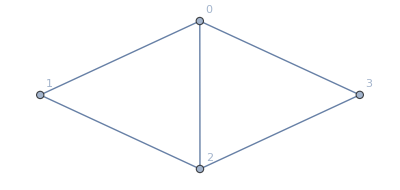

```mathematica
Graph[DualGraph[Faces[allGraphs[29413,"graph"]]],VertexLabels->"Name"]
```

```mathematica
Reduce[x-a>b,x]
```

(a|b)∈Reals&&x>a+b